```mathematica
KdV={D[u[x,t],t]+6 u[x,t]*D[u[x,t],x]+D[u[x,t],{x,3}]==0}
```

{u^(0,1)[x,t]+6 u[x,t] u^(1,0)[x,t]+u^(3,0)[x,t]==0}

```mathematica
{a1,a2,a3}={1,2,1};{b1,b2,b3}={2,1,3};{r1,r2}={5,5};
```

```mathematica
bc1=a1 *(D[u[x,t],{x,2}]/.x->0)+a2*(D[u[x,t],{x,1}]/.x->0)+a3 u[0,t]==0
```

u[0,t]+2 u^(1,0)[0,t]+u^(2,0)[0,t]==0

```mathematica
bc2=b1 *(D[u[x,t],{x,2}]/.x->1)+b2*(D[u[x,t],{x,1}]/.x->1)+b3 u[1,t]==0
```

3 u[1,t]+u^(1,0)[1,t]+2 u^(2,0)[1,t]==0

```mathematica
bc3=r1*(D[u[x,t],{x,1}]/.x->1)+r2*u[1,t]==0
```

5 u[1,t]+5 u^(1,0)[1,t]==0

```mathematica
bc={bc1,bc2,bc3}
```

{u[0,t]+2 u^(1,0)[0,t]+u^(2,0)[0,t]==0,3 u[1,t]+u^(1,0)[1,t]+2 u^(2,0)[1,t]==0,5 u[1,t]+5 u^(1,0)[1,t]==0}

```mathematica
bc3
```

5 u[1,t]+5 u^(1,0)[1,t]==0

```mathematica
ic={u[x,0]==0}
```

{u[x,0]==0}

```mathematica
usol=First[u/.NDSolve[Flatten[{KdV,bc,ic}],u,{x,0,1},{t,0,1}]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[usol[x,t],{x,0,1},{t,0,1},PlotRange->All]
```

-Graphics3D-

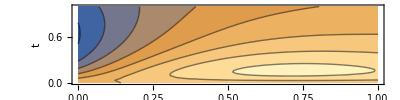

```mathematica
ContourPlot[usol[x,t],{x,0,1},{t,0,1},BaseStyle->FontSize->22,FrameLabel->{"x","t"},PlotLegends->Automatic,LabelStyle->FontSize->18,AspectRatio->1/4]
```

```mathematica
Length[Table[i,{i,0,1,1/10}]]
```

11

```mathematica
For[gridres=10,gridres<110,gridres+=10,
grid=Table[t,{t,0,1,1/gridres}];
tab=Table[usol[x,t],{x,grid},{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","KdV_sln_",ToString[gridres],".csv"],tab]
]
```